```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,115.411},{60,140.999},{70,140.275},{80,132.663},{90,123.918},{100,115.774},{110,108.659},{120,102.58},{130,97.4111},{140,92.9993},{150,89.1967},{160,85.8808},{170,82.9646},{180,80.4014},{190,78.2111},{200,76.7285},{210,57.0565},{220,70.3426},{230,69.2096},{240,67.8348},{250,66.4725},{260,65.1669},{270,63.9265},{280,62.7507},{290,61.6358},{300,60.5775},{310,59.5716},{320,58.6141},{330,57.7014},{340,56.8302},{350,55.9976},{360,55.2011},{370,54.4382},{380,53.707},{390,53.0055},{400,52.3319},{410,51.6849},{420,51.0629},{430,50.4647},{440,49.889},{450,49.3349},{460,48.8012},{470,48.287},{480,47.7915},{490,47.3138},{500,46.8532},{510,46.409},{520,45.9804},{530,45.5669},{540,45.1679},{550,44.7827},{560,44.411},{570,44.052},{580,43.7054},{590,43.3708},{600,43.0476},{610,42.7355},{620,42.4341},{630,42.143},{640,41.8619},{650,41.5903},{660,41.328},{670,41.0747},{680,40.8301},{690,40.5939},{700,40.3658},{710,40.1455},{720,39.9329},{730,39.7276},{740,39.5295},{750,39.3383},{760,39.1537},{770,38.9758},{780,38.8041},{790,38.6385},{800,38.4789},{810,38.3251},{820,38.1769},{830,38.0342},{840,37.8967},{850,37.7644},{860,37.6372},{870,37.5148},{880,37.3972},{890,37.2842},{900,37.1757},{910,37.0717},{920,36.9719},{930,36.8763},{940,36.7848},{950,36.6972},{960,36.6136},{970,36.5337},{980,36.4576},{990,36.3851},{1000,36.3161},{1010,36.2506},{1020,36.1885},{1030,36.1297},{1040,36.0741},{1050,36.0217},{1060,35.9725},{1070,35.9263},{1080,35.8831},{1090,35.8428},{1100,35.8053},{1110,35.7707},{1120,35.7389},{1130,35.7098},{1140,35.6833},{1150,35.6594},{1160,35.6381},{1170,35.6192},{1180,35.6028},{1190,35.5889},{1200,35.5772},{1210,35.5679},{1220,35.5609},{1230,35.556},{1240,35.5533},{1250,35.5527},{1260,35.5542},{1270,35.5577},{1280,35.5631},{1290,35.5704},{1300,35.5796},{1310,35.5906},{1320,35.6033},{1330,35.6176},{1340,35.6335},{1350,35.651},{1360,35.6699},{1370,35.6902},{1380,35.7118},{1390,35.7346},{1400,35.7585},{1410,35.7835},{1420,35.8094},{1430,35.8361},{1440,35.8635},{1450,35.8915},{1460,35.92},{1470,35.9488},{1480,35.9778},{1490,36.0069},{1500,36.0358},{1510,36.0644},{1520,36.0926},{1530,36.1201},{1540,36.1468},{1550,36.1724},{1560,36.1968},{1570,36.2197},{1580,36.2408},{1590,36.2601},{1600,36.2771},{1610,36.2917},{1620,36.3035},{1630,36.3124},{1640,36.3181},{1650,36.3202},{1660,36.3186},{1670,36.3128},{1680,36.3026},{1690,36.2874},{1700,36.2667},{1710,36.2395},{1720,36.2042},{1730,36.158},{1740,36.0952},{1750,36.004}}

{{50,0.00115411},{60,0.00140999},{70,0.00140275},{80,0.00132663},{90,0.00123918},{100,0.00115774},{110,0.00108659},{120,0.0010258},{130,0.000974111},{140,0.000929993},{150,0.000891967},{160,0.000858808},{170,0.000829646},{180,0.000804014},{190,0.000782111},{200,0.000767285},{210,0.000570565},{220,0.000703426},{230,0.000692096},{240,0.000678348},{250,0.000664725},{260,0.000651669},{270,0.000639265},{280,0.000627507},{290,0.000616358},{300,0.000605775},{310,0.000595716},{320,0.000586141},{330,0.000577014},{340,0.000568302},{350,0.000559976},{360,0.000552011},{370,0.000544382},{380,0.00053707},{390,0.000530055},{400,0.000523319},{410,0.000516849},{420,0.000510629},{430,0.000504647},{440,0.00049889},{450,0.000493349},{460,0.000488012},{470,0.00048287},{480,0.000477915},{490,0.000473138},{500,0.000468532},{510,0.00046409},{520,0.000459804},{530,0.000455669},{540,0.000451679},{550,0.000447827},{560,0.00044411},{570,0.00044052},{580,0.000437054},{590,0.000433708},{600,0.000430476},{610,0.000427355},{620,0.000424341},{630,0.00042143},{640,0.000418619},{650,0.000415903},{660,0.00041328},{670,0.000410747},{680,0.000408301},{690,0.000405939},{700,0.000403658},{710,0.000401455},{720,0.000399329},{730,0.000397276},{740,0.000395295},{750,0.000393383},{760,0.000391537},{770,0.000389758},{780,0.000388041},{790,0.000386385},{800,0.000384789},{810,0.000383251},{820,0.000381769},{830,0.000380342},{840,0.000378967},{850,0.000377644},{860,0.000376372},{870,0.000375148},{880,0.000373972},{890,0.000372842},{900,0.000371757},{910,0.000370717},{920,0.000369719},{930,0.000368763},{940,0.000367848},{950,0.000366972},{960,0.000366136},{970,0.000365337},{980,0.000364576},{990,0.000363851},{1000,0.000363161},{1010,0.000362506},{1020,0.000361885},{1030,0.000361297},{1040,0.000360741},{1050,0.000360217},{1060,0.000359725},{1070,0.000359263},{1080,0.000358831},{1090,0.000358428},{1100,0.000358053},{1110,0.000357707},{1120,0.000357389},{1130,0.000357098},{1140,0.000356833},{1150,0.000356594},{1160,0.000356381},{1170,0.000356192},{1180,0.000356028},{1190,0.000355889},{1200,0.000355772},{1210,0.000355679},{1220,0.000355609},{1230,0.00035556},{1240,0.000355533},{1250,0.000355527},{1260,0.000355542},{1270,0.000355577},{1280,0.000355631},{1290,0.000355704},{1300,0.000355796},{1310,0.000355906},{1320,0.000356033},{1330,0.000356176},{1340,0.000356335},{1350,0.00035651},{1360,0.000356699},{1370,0.000356902},{1380,0.000357118},{1390,0.000357346},{1400,0.000357585},{1410,0.000357835},{1420,0.000358094},{1430,0.000358361},{1440,0.000358635},{1450,0.000358915},{1460,0.0003592},{1470,0.000359488},{1480,0.000359778},{1490,0.000360069},{1500,0.000360358},{1510,0.000360644},{1520,0.000360926},{1530,0.000361201},{1540,0.000361468},{1550,0.000361724},{1560,0.000361968},{1570,0.000362197},{1580,0.000362408},{1590,0.000362601},{1600,0.000362771},{1610,0.000362917},{1620,0.000363035},{1630,0.000363124},{1640,0.000363181},{1650,0.000363202},{1660,0.000363186},{1670,0.000363128},{1680,0.000363026},{1690,0.000362874},{1700,0.000362667},{1710,0.000362395},{1720,0.000362042},{1730,0.00036158},{1740,0.000360952},{1750,0.00036004}}

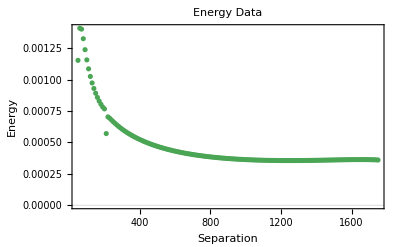

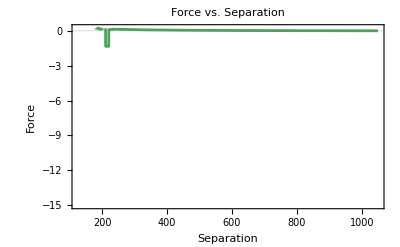

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

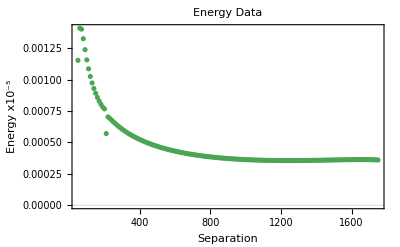

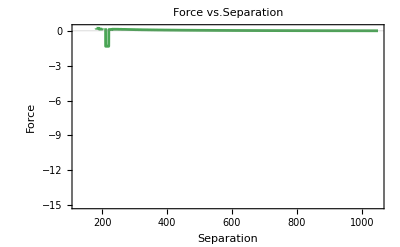

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
Close[stream];
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
|
```